## Universal

Check constants and get the inverse function for the discrete distribution.  Start by using integration to obtain the appropriate form for the CDF.

```mathematica
Integrate[1/(x Log[x]^2),x]
```

-1/Log[x]

Need to obtain the normalizing constant.  Normalize for j = 1,2,....  Flip so that subtract so that get the right limit as arguments increase.

```mathematica
Clear[F,Finv,f];


Unprotect[K,δ];Clear[K,δ];
    K[1]=1/2.10974;K[2]=1/1.06906;K[3]=1/0.79288;
 Protect[K,δ];

F[j_] :=K[δ]/Log[j+δ];
Finv[p_] := Exp[K[δ]/p]-δ;
f[j_] := K[δ]/((j+δ)(Log[j+δ])^2)
```

The expression simplifies nicely, and has the vague form (albeit wrong signs) as that produced by the harmonic.

```mathematica
h[w,σ]
```

ⅇ^(w/σ) σ

```mathematica
g[w_,σ_] =FullSimplify[σ f[Finv[w/σ]]/. K[δ]->1, {σ>0,w>0,σ/(w-σ)∈ Reals}]
```

(ⅇ^(-σ/w) w^2)/σ

Do you ever spend too much?  

Yes, if wealth is large.  The crossover occurs where log(x) = 1/x ≈ 1.76.  Larger choice for the scaling term push that wealth farther out. A further useful reason to increase the σ parameter.

```mathematica
zz=1/ProductLog[1.]
```

1.76322

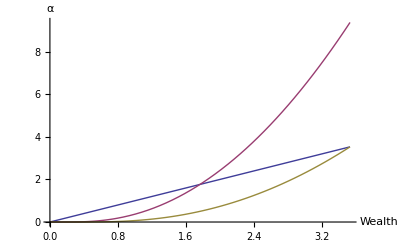

```mathematica
Plot[{w,g[w,1],g[w,2]},{w,0.001,2 zz},
AxesLabel->{"Wealth","α"}]
```

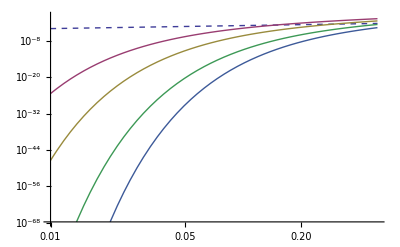

```mathematica
LogLogPlot[{0.01w,g[w,0.5],g[w,1],g[w,2],g[w,3]},{w,0.01,0.5},
PlotStyle->{
Dashing[0.01],
Dashing[None], Dashing[None],
Dashing[None], Dashing[None]}
]
```

```mathematica
FullSimplify[σ f[Finv[w/σ]]/. K[δ]->3, {σ>0,w>0,σ/(w-σ)∈ Reals}]
```

(ⅇ^(-(3 σ)/w) w^2)/(3 σ)

## Geometric

Define the geometric density with spending rate ψ and its inverse.  Note that it’s got an ugly inverse function.

```mathematica
Clear[g,K]
g[x_,ψ_]=K+Integrate[-ψ(1-ψ)^(x-1),x]
```

K-((1-ψ)^(-1+x) ψ)/Log[1-ψ]

```mathematica
Clear[h];
h[y_,ψ_]:= 1+(Log[-Log[1-ψ]]-Log[ψ]+Log[y-K])/Log[1-ψ]
```

```mathematica
FullSimplify[h[g[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

```mathematica
FullSimplify[g[h[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

For a simpler form, MM pushes terms into the log.

```mathematica
Clear[y,ψ]
FullSimplify[h[y,ψ],{x>0,ψ>0, ψ<1}]
```

Log[-((K-y) (-1+ψ) Log[1-ψ])/ψ]/Log[1-ψ]

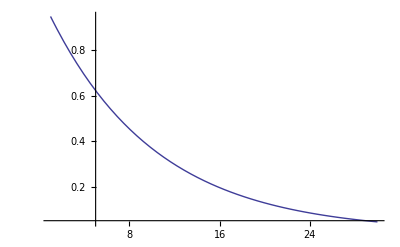

```mathematica
Plot[g[x,0.1],{x,1,30}, PlotRange->All]
```

```mathematica
Finv[f_] :=With[{z=Log[1-ψ]},
Log[f (ψ-1)z/ψ]/z]
f[x_] :=ψ(1-ψ)^(x-1)
```

```mathematica
Finv[w/σ]
```

Log[(w (-1+ψ) Log[1-ψ])/(σ ψ)]/Log[1-ψ]

```mathematica
σ f[Finv[w/σ]]
```

(w (-1+ψ) Log[1-ψ])/(1-ψ)

## Harmonic

```mathematica
Clear[f, Finv];
Finv[f_]:=ⅇ^-f
f[x_] := 1/x
```

Reduces to an exponential (but with wrong sign!)

```mathematica
h[w_,σ_]=σ f[Finv[w/σ]]
```

ⅇ^(w/σ) σ

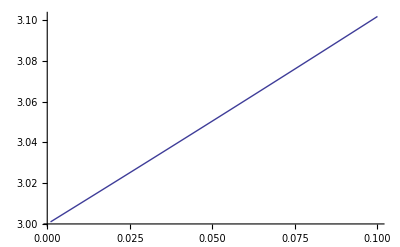

```mathematica
With[{σ=3},
Plot[σ f[Finv[w/σ]],{w,0.001,0.1}]]
```